```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

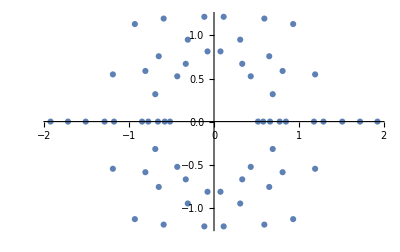

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
fastRootCalculate[n_Integer]:=With[{
poly=1+Map[{1}~Join~#&,Tuples[{1,-1},n-1]].#^Range[n]&,mix=If[n>3,Thread,Identity]@Join[#,-#]&,
map=If[n>5,ParallelMap,Map]@##&},
With[{k=Floor[n/4]-$KernelCount},If[k>0,LaunchKernels@k]];
{x}~Module~mix@map[NSolveValues[#==0,x]&,poly@x]
](* use x/.NSolve if NSolveValues is not supported *)
```

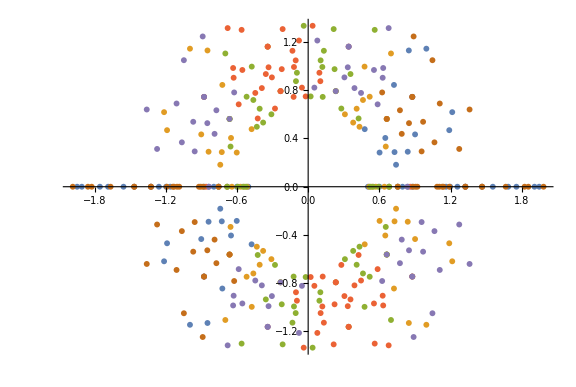

```mathematica
ComplexListPlot[fastRootCalculate[6],ImageSize->Large]
```

```mathematica
Block[{t},AbsoluteTiming[t=fastRootCalculate[16];]]
```

{49.2826,Null}

```mathematica
displayRoots[n_]:=With[{
p=fastRootCalculate[n],
s=AbsolutePointSize@If[n>15,1/(n-14),16-n],
l=Style[Row@{"n = ",n},FontSize->21+3n],
c=2^{1,.5}+.02},
ComplexListPlot@@{p,ImageSize->840+120n,Axes->n<6,PlotStyle->s,
PlotLabel->l,PlotRange->{-#,#}&/@c,AspectRatio->Tr@Ratios@c}]
```

```mathematica
Block[{g,t={0,0}},
t[[1]]=AbsoluteTiming[g=Array[displayRoots,15];];
t[[2]]=AbsoluteTiming[Do[Export[ToString@i<>".png",g[[i]]],{i,Length@g}]];
t]
```

{{64.1111,Null},{8.14141,Null}}

```mathematica
Block[{t=Array[Graphics[]&,15]},
Do[t[[i-1]]=displayRoots[i],{i,2,Length[t]+1}];
Export["littlewood.gif",t,"DisplayDurations"->1]];
```

```mathematica
RGBColor@@@Tuples[{1,1/2,0},3]
```

{RGBColor[1, 1, 1],RGBColor[1, 1, Rational[1, 2]],RGBColor[1, 1, 0],RGBColor[1, Rational[1, 2], 1],RGBColor[1, Rational[1, 2], Rational[1, 2]],RGBColor[1, Rational[1, 2], 0],RGBColor[1, 0, 1],RGBColor[1, 0, Rational[1, 2]],RGBColor[1, 0, 0],RGBColor[Rational[1, 2], 1, 1],RGBColor[Rational[1, 2], 1, Rational[1, 2]],RGBColor[Rational[1, 2], 1, 0],RGBColor[Rational[1, 2], Rational[1, 2], 1],RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, 1],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], 0, 0],RGBColor[0, 1, 1],RGBColor[0, 1, Rational[1, 2]],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], 1],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, Rational[1, 2], 0],RGBColor[0, 0, 1],RGBColor[0, 0, Rational[1, 2]],RGBColor[0, 0, 0]}